```mathematica
ClearAll["Global`*"]
```

```mathematica
V1O={x1-1,y1};
V2O={x2-1,y2};
V3O={x3-1,y3};
VI1={-1-x1,-y1};
VI2={-1-x2,-y2};
VI3={-1-x3,-y3};
V12={x1-x2,y1-y2};
V23={x2-x3,y2-y3};
V13={x1-x3,y1-y3};
CI1={x1-1,y1}/2;
CI2={x2-1,y2}/2;
CI3={x3-1,y3}/2;
C1O={x1+1,y1}/2;
C2O={x2+1,y2}/2;
C3O={x3+1,y3}/2;
C12={x1+x2,y1+y2}/2;
C13={x1+x3,y1+y3}/2;
C23={x2+x3,y2+y3}/2;
```

```mathematica
LPlot2[pspre_]:=LPlot[{{{x1,y1}},{{x2,y2}},{{x3,y3}}}/.pspre[[2]]]
LPlot[ps_]:=ListPlot[Flatten[{ps,{{{-1,0},{1,0}}}},1],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->{Red,Green,Blue,Black},AspectRatio->1]
```

#### Other

```mathematica
(*sum2[p_,n_:1,t_:1]:=n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+t*(Norm[CI1-CI2]^-p+Norm[CI1-C1O]^-p+Norm[CI1-C2O]^-p+Norm[CI2-C1O]^-p+Norm[CI2-C2O]^-p+Norm[C1O-C2O]^-p)
sum3[p_,n_:1,t_:1]:=n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+t*(Norm[CI1-C12]^-p+Norm[CI1-C2O]^-p+Norm[C12-C2O]^-p)
sum4[p_,n_:1,t_:1]:=n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+t*(Norm[CI1-CI2]^-p+Norm[CI1-CI3]^-p+Norm[CI1-C1O]^-p+Norm[CI1-C2O]^-p+Norm[CI1-C3O]^-p+Norm[CI2-CI3]^-p+Norm[CI2-C1O]^-p+Norm[CI2-C2O]^-p+Norm[CI2-C3O]^-p+Norm[CI3-C1O]^-p+Norm[CI3-C2O]^-p+Norm[CI3-C3O]^-p+Norm[C1O-C2O]^-p+Norm[C1O-C3O]^-p+Norm[C2O-C3O]^-p)
sum5[p_,n_:1,t_:1]:=n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+t*(Norm[CI1-C12]^-p+Norm[CI1-C23]^-p+Norm[CI1-C3O]^-p+Norm[C12-C23]^-p+Norm[C12-C3O]^-p+Norm[C23-C3O]^-p)
sum6[p_,n_:1,t_:1]:=n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*(Norm[CI1-C12]^-p+Norm[CI1-C23]^-p+Norm[CI1-C3O]^-p+Norm[C12-C23]^-p+Norm[C12-C3O]^-p+Norm[C23-C3O]^-p+Norm[CI1-C13]^-p+Norm[C12-C13]^-p+Norm[C23-C13]^-p+Norm[C3O-C13]^-p)*)
(*sum2[p_,n_:1,t_:1]:=t*(Norm[V1O]^-p+Norm[VI1]^-p+Norm[V2O]^-p+Norm[VI2]^-p)+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+t*(Norm[CI1-CI2]^-p+Norm[CI1-C1O]^-p+Norm[CI2-C2O]^-p+Norm[C1O-C2O]^-p)
sum3[p_,n_:1,t_:1]:=t*(Norm[VI1]^-p+Norm[V2O]^-p)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+t*(Norm[CI1-C12]^-p+Norm[C12-C2O]^-p)
sum4[p_,n_:1,t_:1]:=t*(Norm[V1O]^-p+Norm[VI1]^-p+Norm[V2O]^-p+Norm[VI2]^-p+Norm[V3O]^-p+Norm[VI3]^-p)+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+t*(Norm[CI1-CI2]^-p+Norm[CI1-CI3]^-p+Norm[CI1-C1O]^-p+Norm[CI2-CI3]^-p+Norm[CI2-C2O]^-p+Norm[CI3-C3O]^-p+Norm[C1O-C2O]^-p+Norm[C1O-C3O]^-p+Norm[C2O-C3O]^-p)
sum5[p_,n_:1,t_:1]:=t*(Norm[VI1]^p+Norm[V3O]^-p)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+t*(Norm[CI1-C12]^-p+Norm[C12-C23]^-p+Norm[C23-C3O]^-p)
sum6[p_,n_:1,t_:1]:=t*(Norm[VI1]^-p+Norm[V3O]^-p)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*(Norm[CI1-C12]^-p+Norm[C12-C23]^-p+Norm[C23-C3O]^-p+Norm[CI1-C13]^-p+Norm[C12-C13]^-p+Norm[C23-C13]^-p+Norm[C3O-C13]^-p)*)
(*sum2[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3)+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+t*(Norm[VI1]^-p2+Norm[VI2]^-p2+Norm[V1O]^-p2+Norm[V12]^-p2+Norm[V2O]^-p2)/(Norm[VI1]+Norm[VI2]+Norm[V1O]+Norm[V12]+Norm[V2O])^-p2
sum3[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+t*(Norm[VI1]^-p2+Norm[VI2]^-p2+Norm[V1O]^-p2+Norm[V12]^-p2+Norm[V2O]^-p2)/(Norm[VI1]+Norm[VI2]+Norm[V1O]+Norm[V12]+Norm[V2O])^-p2
sum4[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3+Abs[x3]^p3)+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+t*sum[-p2]/sum[1]^-p2
sum5[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3+Abs[x3]^p3)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+t*sum[-p2]/sum[1]^-p2
sum6[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3+Abs[x3]^p3)+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*sum[-p2]/sum[1]^-p2
sum7[p_,p2_,p3_,n_:1,t_:1,g_:1]:=g*(Abs[x1]^p3+Abs[x2]^p3+Abs[x3]^p3)+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p+Norm[V13]^p)+t*sum[-p2]/sum[1]^-p2*)
(*sumN2[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[V12]^p)/5;
sumN3[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[V3O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[VI3]^p+Norm[V12]^p+Norm[V13]^p+Norm[V23]^p)/9;
sum2[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3)/sumN2[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+t*(Abs[Norm[VI1]-sumN2[1]]^p2+Abs[Norm[VI2]-sumN2[1]]^p2+Abs[Norm[V1O]-sumN2[1]]^p2+Abs[Norm[V2O]-sumN2[1]]^p2)+r*Norm[V12]^-p4/sumN2[1]^-p4
sum3[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN2[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+t*(Abs[Norm[V12]-sumN2[1]]^p2+Abs[Norm[VI1]-sumN2[1]]^p2+Abs[Norm[V2O]-sumN2[1]]^p2)+r*(Norm[V1O]^-p4+Norm[VI2]^-p4)/sumN2[1]^-p4
sum4[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3+Norm[V3O]^-p3+Norm[VI3]^-p3)/sumN3[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[VI2]-sumN3[1]]^p2+Abs[Norm[V1O]-sumN3[1]]^p2+Abs[Norm[V2O]-sumN3[1]]^p2+Abs[Norm[VI3]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2)+r*(Norm[V12]^-p4+Norm[V13]^-p4+Norm[V23]^-p4)/sumN3[1]^-p4
sum5[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN3[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[V12]-sumN3[1]]^p2+Abs[Norm[V23]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2)+r*(Norm[VI2]^-p4+Norm[VI3]^-p4+Norm[V1O]^-p4+Norm[V13]^-p4+Norm[V2O]^-p4)/sumN3[1]^-p4
sum6[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN3[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[V12]-sumN3[1]]^p2+Abs[Norm[V23]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[VI2]^-p4+Norm[VI3]^-p4+Norm[V1O]^-p4+Norm[V2O]^-p4)/sumN3[1]^-p4
sum7[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3+Norm[V3O]^-p3+Norm[VI3]^-p3)/sumN3[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[VI2]-sumN3[1]]^p2+Abs[Norm[V1O]-sumN3[1]]^p2+Abs[Norm[V2O]-sumN3[1]]^p2+Abs[Norm[VI3]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[V12]^-p4+Norm[V23]^-p4)/sumN3[1]^-p4*)
```

#### More

```mathematica
sumN2[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[V12]^p)/5;
sumN3[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[V3O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[VI3]^p+Norm[V12]^p+Norm[V13]^p+Norm[V23]^p)/9;
sum2[p_,p3_,p4_,n_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3)/sumN2[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+r*(Norm[V12]^-p4)
sum3[p_,p3_,p4_,n_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN2[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+r*(Norm[VI2]^-p4+Norm[V1O]^-p4)
sum4[p_,p3_,p4_,n_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3+Norm[V3O]^-p3+Norm[VI3]^-p3)/sumN3[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+r*(Norm[V12]^-p4+Norm[V13]^-p4+Norm[V23]^-p4)*2
sum5[p_,p3_,p4_,n_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN3[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+r*(Norm[VI2]^-p4+Norm[V13]^-p4+Norm[V2O]^-p4)
sum6[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN3[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[V12]-sumN3[1]]^p2+Abs[Norm[V23]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[VI2]^-p4+Norm[VI3]^-p4+Norm[V1O]^-p4+Norm[V2O]^-p4)/sumN3[1]^-p4
sum7[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3+Norm[V3O]^-p3+Norm[VI3]^-p3)/sumN3[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[VI2]-sumN3[1]]^p2+Abs[Norm[V1O]-sumN3[1]]^p2+Abs[Norm[V2O]-sumN3[1]]^p2+Abs[Norm[VI3]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[V12]^-p4+Norm[V23]^-p4)/sumN3[1]^-p4
```

{6.,{x1→-1.35105×10^-8,x2→-1.13695×10^-8,x3→-7.72126×10^-9,y1→-2.08104×10^-8,y2→-1.74042×10^-8,y3→-1.89778×10^-8}}

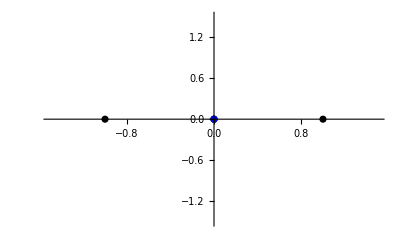

{6.,{x1→-0.979988,x2→-0.979988,x3→-0.979988,y1→5.88105×10^-8,y2→5.88104×10^-8,y3→5.88109×10^-8}}

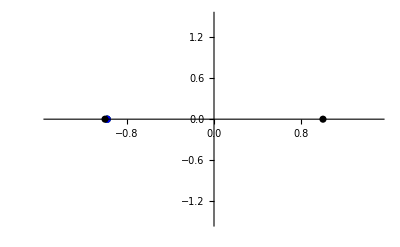

{5.69519,{x1→1.,x2→1.,x3→-1.,y1→-1.,y2→1.,y3→1.}}

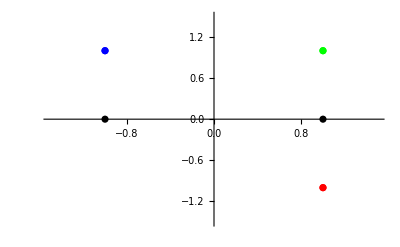

{4.05,{x1→1.,x2→1.06954×10^-7,x3→-1.,y1→1.,y2→-1.,y3→1.}}

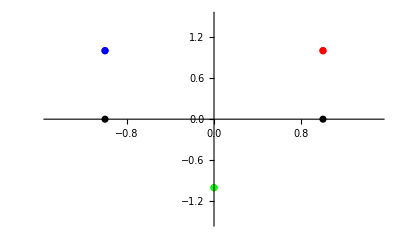

{18.4617,{x1→0.381781,x2→-1.61966×10^-8,x3→-0.381781,y1→0.623473,y2→-0.28849,y3→0.623473}}

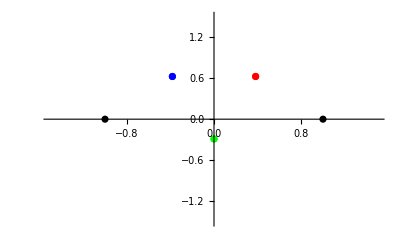

{18.8052,{x1→-0.174499,x2→-0.174499,x3→0.264646,y1→-0.410794,y2→0.410794,y3→-1.84056×10^-8}}

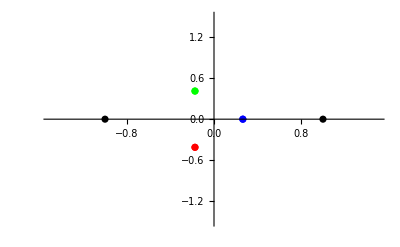

{17.7845,{x1→5.14201×10^-9,x2→0.505959,x3→-0.505959,y1→-0.337979,y2→0.947256,y3→0.947256}}

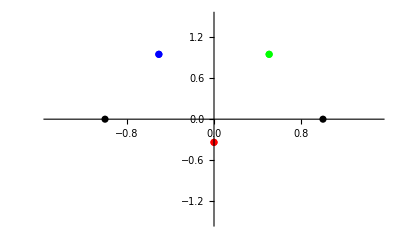

```mathematica
NMinimize[{sum[2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1]+sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1]+sum[2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-2]+sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
```

```mathematica
sum4[2,1,1,1]/.{Abs[X_]->X};
%//Expand;
%/.{x1->0,x2->0,x3->0,y1->-0.86,y2->0.86,y3->0,n->1,t2->1}
```

94.0385

{7.92332,{x1→-1.04356×10^-8,x2→-8.19006×10^-9,y1→0.119443,y2→-0.119443}}

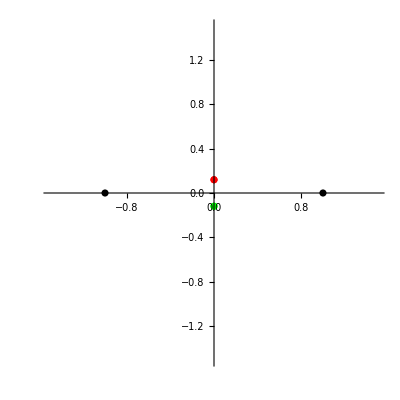

{3.21146,{x1→-0.199169,x2→0.199169,y1→-5.50258×10^-9,y2→-1.3506×10^-8}}

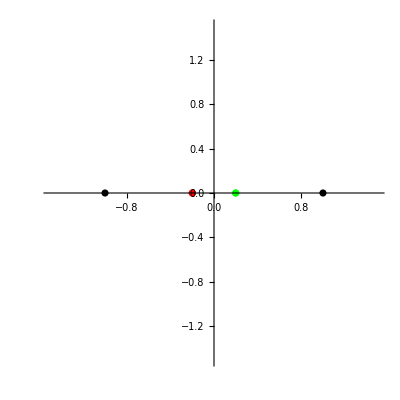

{13.1603,{x1→-2.38333×10^-8,x2→-2.5809×10^-8,x3→4.97787×10^-8,y1→-0.266013,y2→0.266013,y3→-1.62221×10^-9}}

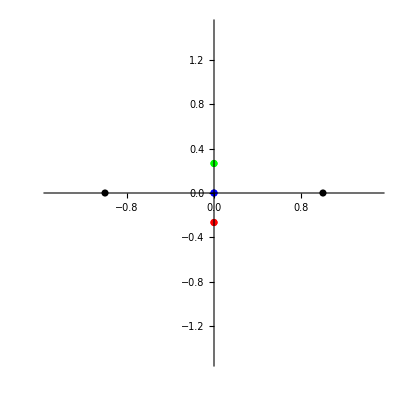

{2.68164,{x1→-0.248194,x2→-0.126606,x3→0.402989,y1→-4.23975×10^-8,y2→-4.22703×10^-8,y3→-2.56391×10^-8}}

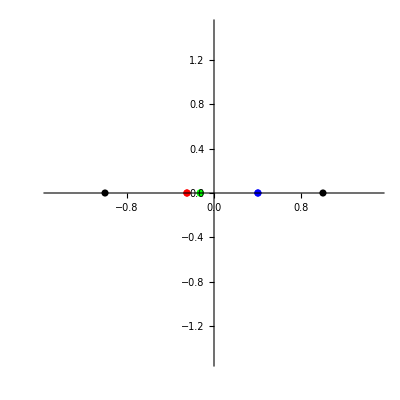

{4.90958,{x1→-0.291231,x2→-6.45039×10^-9,x3→0.291231,y1→1.44749×10^-8,y2→4.4581×10^-8,y3→1.43076×10^-8}}

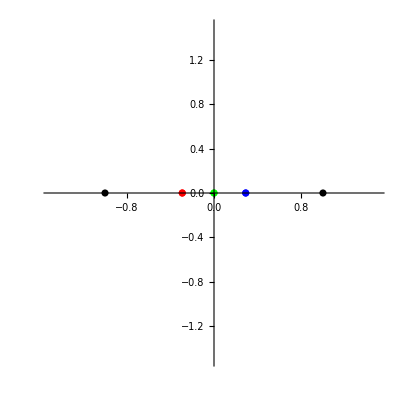

{9.89131,{x1→-0.111856,x2→1.82974×10^-8,x3→0.111856,y1→0.262087,y2→-0.497824,y3→0.262087}}

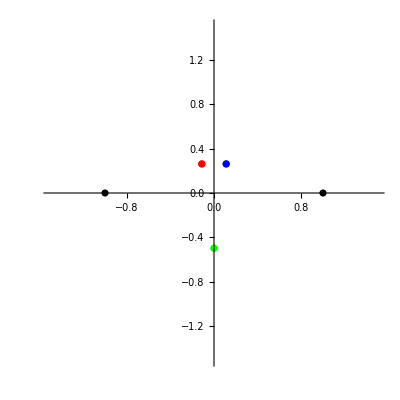

```mathematica
NMinimize[{sum2[4,1,1,1,0.1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[y1]<=1,Abs[y2]<=1},{x1,x2,y1,y2}]
LPlot2[%]
NMinimize[{sum3[4,1,1,1,0.1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[y1]<=1,Abs[y2]<=1},{x1,x2,y1,y2}]
LPlot2[%]
NMinimize[{sum4[4,1,1,1,0.1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum5[4,1,1,1,0.1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum6[2,2,1,1,1,1,1,0],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum7[2,2,1,1,1,1,1,0],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
```